### Categorization

Tutorial

PaperPlot

PaperPlot`

PaperPlot/tutorial/Plotting with PaperPlot

### Keywords

Details

# Plotting with PaperPlot

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Minimal tutorial

Make sure you have the "LM Roman 10" font: http://www.gust.org.pl/projects/e-foundry/latin-modern/download

```mathematica
Needs["PaperPlot`"]
```

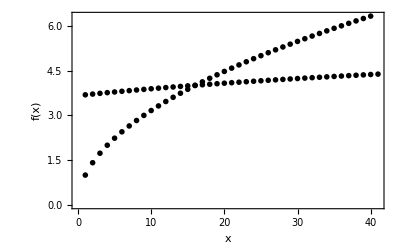

```mathematica
ListPlot[{Sqrt[Range[40]],Log[Range[40,80]]},FrameLabel->{"x","f(x)"},PlotTheme->"MonoPaper"]
```

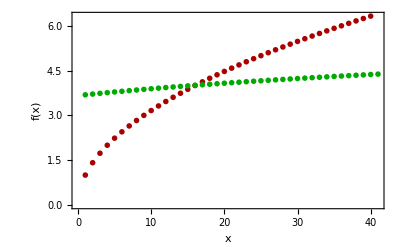

```mathematica
ListPlot[{Sqrt[Range[40]],Log[Range[40,80]]},FrameLabel->{"x","f(x)"},PlotTheme->"ColorPaper"]
```

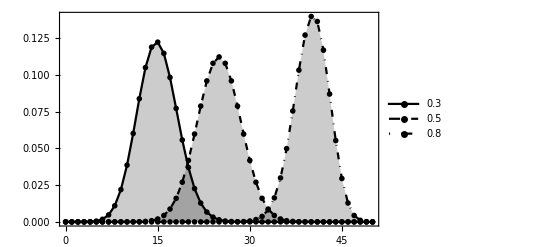

```mathematica
ListPlot[Table[{k,PDF[BinomialDistribution[50,p],k]},{p,{0.3,0.5,0.8}},{k,0,50}],Filling->Axis,PlotLegends->{0.3,0.5,0.8},PlotTheme->"MonoPaper",Joined->True]
```

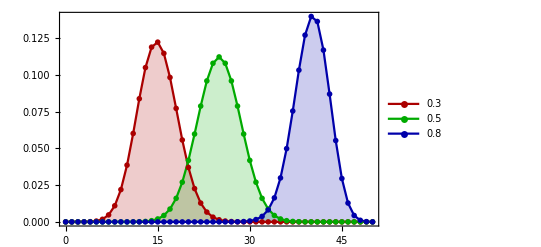

```mathematica
ListPlot[Table[{k,PDF[BinomialDistribution[50,p],k]},{p,{0.3,0.5,0.8}},{k,0,50}],Filling->Axis,PlotLegends->{0.3,0.5,0.8},PlotTheme->"ColorPaper",Joined->True]
```

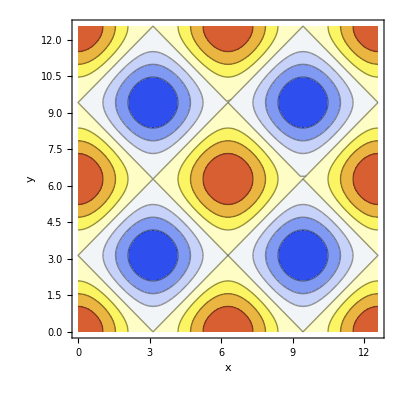

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},PlotTheme->"ColorPaper",FrameLabel->{"x","y","Cos(x)+Cos(y)"}]
```

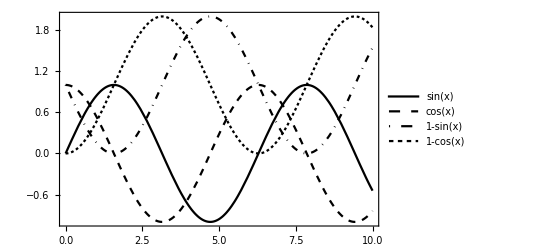

```mathematica
Plot[{Sin[x],Cos[x],1-Sin[x],1-Cos[x]},{x,0,10},PlotTheme->"MonoPaper",PlotLegends->"Expressions"]
```

Dashing is not enabled by default in ColorPaper...

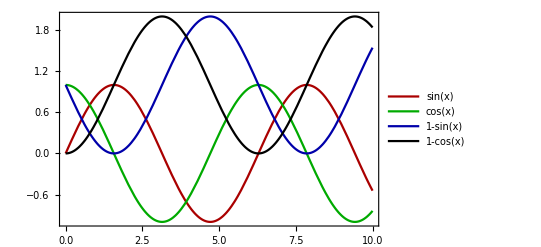

```mathematica
Plot[{Sin[x],Cos[x],1-Sin[x],1-Cos[x]},{x,0,10},PlotTheme->"ColorPaper",PlotLegends->"Expressions"]
```

... but you can add it if you want.

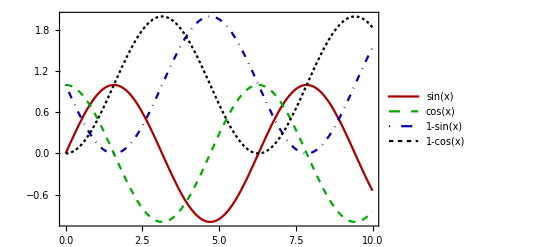

```mathematica
Plot[{Sin[x],Cos[x],1-Sin[x],1-Cos[x]},{x,0,10},PlotTheme->"ColorPaper",PlotStyle->PaperDashing,PlotLegends->"Expressions"]
```

Try it with the ErrorPlot package

```mathematica
Needs["ErrorPlot`"]
```

```mathematica
data=Table[{x,x+1,Integrate[t^2,{t,x,x+1}],2*Sqrt[Integrate[t^4,{t,x,x+1}]-Integrate[t^2,{t,x,x+1}]^2]},{x,1,20,5}];
data2=Table[{x,x+1,Integrate[t^2,{t,x,x+1}],2*Sqrt[Integrate[t^4,{t,x,x+1}]-Integrate[t^2,{t,x,x+1}]^2]},{x,3,20,5}];
```

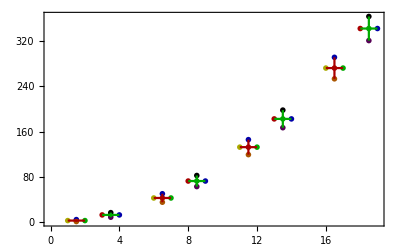

```mathematica
ErrorPlot[{data,data2},PlotErrorBars->{True,True},PlotTheme->"ColorPaper"]
```

More About

Related Tutorials

Related Wolfram Education Group Courses